```mathematica
ClearAll["Global`*"]
```

```mathematica
F1[n_,1]:= F1[n,1]=Mod[n,4]; F1[1,1]:=0
f1[n_,1] := f1[n,1]=F1[n,1]-F1[n-1,1]
f1[n_,k_] := f1[n,k]=F1[n,k]-F1[n-1,k]
f1[1,0] := 1
F1[n_,0]:=F1[n,0]=1
F1[n_, k_] := F1[n,k] = Sum[ f1[j,1]F1[Floor[n/j],k-1],{j,2,n}]
expf[n_] := Sum[ 1/(k!) f1[n,k],{k,0,Log[2,n]}]
Ex1[n_, 0] := 1; Ex1[n_, k_] := Ex1[n,k] = Sum[ expf[j] Ex1[ Floor[n/j], k-1],{j,1,n}]
ex1[n_, k_] := ex1[n,k]=Ex1[n,k]-Ex1[n-1,k]
Ex2[n_,k_] := Ex2[n,k]=Sum[(-1)^j Binomial[k,j] Ex1[n,k-j],{j,0,k}]
EF2[n_] := Sum[ (-1)^(k+1)/k Ex2[n,k],{k,1,Log[2,n]}]
```

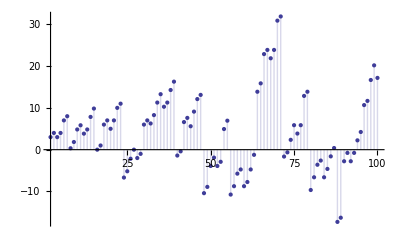

```mathematica
DiscretePlot[{Ex1[n,1]},{n,2,100}]
```

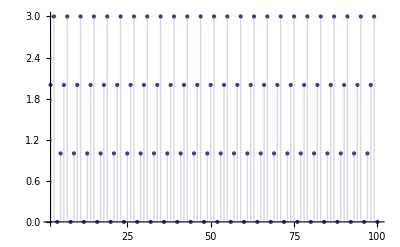

```mathematica
DiscretePlot[EF2[n],{n,2,100}]
```

```mathematica
Table[ {n,F1[n,1], EF2[n]},{n,1,100}]//TableForm
```

1 | 0 | 0
2 | 2 | 2
3 | 3 | 3
4 | 0 | 0
5 | 1 | 1
6 | 2 | 2
7 | 3 | 3
8 | 0 | 0
9 | 1 | 1
10 | 2 | 2
11 | 3 | 3
12 | 0 | 0
13 | 1 | 1
14 | 2 | 2
15 | 3 | 3
16 | 0 | 0
17 | 1 | 1
18 | 2 | 2
19 | 3 | 3
20 | 0 | 0
21 | 1 | 1
22 | 2 | 2
23 | 3 | 3
24 | 0 | 0
25 | 1 | 1
26 | 2 | 2
27 | 3 | 3
28 | 0 | 0
29 | 1 | 1
30 | 2 | 2
31 | 3 | 3
32 | 0 | 0
33 | 1 | 1
34 | 2 | 2
35 | 3 | 3
36 | 0 | 0
37 | 1 | 1
38 | 2 | 2
39 | 3 | 3
40 | 0 | 0
41 | 1 | 1
42 | 2 | 2
43 | 3 | 3
44 | 0 | 0
45 | 1 | 1
46 | 2 | 2
47 | 3 | 3
48 | 0 | 0
49 | 1 | 1
50 | 2 | 2
51 | 3 | 3
52 | 0 | 0
53 | 1 | 1
54 | 2 | 2
55 | 3 | 3
56 | 0 | 0
57 | 1 | 1
58 | 2 | 2
59 | 3 | 3
60 | 0 | 0
61 | 1 | 1
62 | 2 | 2
63 | 3 | 3
64 | 0 | 0
65 | 1 | 1
66 | 2 | 2
67 | 3 | 3
68 | 0 | 0
69 | 1 | 1
70 | 2 | 2
71 | 3 | 3
72 | 0 | 0
73 | 1 | 1
74 | 2 | 2
75 | 3 | 3
76 | 0 | 0
77 | 1 | 1
78 | 2 | 2
79 | 3 | 3
80 | 0 | 0
81 | 1 | 1
82 | 2 | 2
83 | 3 | 3
84 | 0 | 0
85 | 1 | 1
86 | 2 | 2
87 | 3 | 3
88 | 0 | 0
89 | 1 | 1
90 | 2 | 2
91 | 3 | 3
92 | 0 | 0
93 | 1 | 1
94 | 2 | 2
95 | 3 | 3
96 | 0 | 0
97 | 1 | 1
98 | 2 | 2
99 | 3 | 3
100 | 0 | 0

```mathematica
Table[ {n,Ex1[n,1]},{n,1,100}]//TableForm
```

1 | 1
2 | 3
3 | 4
4 | 3
5 | 4
6 | 7
7 | 8
8 | 1/3
9 | 11/6
10 | 29/6
11 | 35/6
12 | 23/6
13 | 29/6
14 | 47/6
15 | 59/6
16 | 0
17 | 1
18 | 6
19 | 7
20 | 5
21 | 7
22 | 10
23 | 11
24 | -20/3
25 | -31/6
26 | -13/6
27 | 0
28 | -2
29 | -1
30 | 6
31 | 7
32 | 94/15
33 | 124/15
34 | 169/15
35 | 199/15
36 | 154/15
37 | 169/15
38 | 214/15
39 | 244/15
40 | -7/5
41 | -2/5
42 | 33/5
43 | 38/5
44 | 28/5
45 | 91/10
46 | 121/10
47 | 131/10
48 | -52/5
49 | -89/10
50 | -39/10
51 | -19/10
52 | -39/10
53 | -29/10
54 | 74/15
55 | 104/15
56 | -161/15
57 | -131/15
58 | -86/15
59 | -71/15
60 | -131/15
61 | -116/15
62 | -71/15
63 | -37/30
64 | 1247/90
65 | 1427/90
66 | 2057/90
67 | 2147/90
68 | 1967/90
69 | 2147/90
70 | 2777/90
71 | 2867/90
72 | -74/45
73 | -29/45
74 | 106/45
75 | 527/90
76 | 347/90
77 | 527/90
78 | 1157/90
79 | 1247/90
80 | -434/45
81 | -2377/360
82 | -1297/360
83 | -937/360
84 | -2377/360
85 | -1657/360
86 | -577/360
87 | 143/360
88 | -6217/360
89 | -5857/360
90 | -997/360
91 | -277/360
92 | -997/360
93 | -277/360
94 | 803/360
95 | 1523/360
96 | 3839/360
97 | 4199/360
98 | 5999/360
99 | 7259/360
100 | 6179/360